WOLFRAM LANGUAGE

# Things to Try

This document is a live Wolfram Notebook that mixes text and code.  
Run any piece of code by clicking inside the code, then press " ""shift"" "" ""enter"" " .

Compute 2+2 (just click in the input below and press  " ""shift"" "" ""enter"" "):
    ↓

```mathematica
2+2
```

Make a list of numbers up to 100:

```mathematica
Range[100]
```

Make a list of the first 100 prime numbers:

```mathematica
Table[Prime[n],{n,100}]
```

Also plot the values:

```mathematica
ListPlot[Table[Prime[n],{n,100}]]
```

Get a list of common words in English:

```mathematica
WordList[]
```

Compute the length of each word:

```mathematica
StringLength[WordList[]]
```

Make a histogram of the lengths:

```mathematica
Histogram[StringLength[WordList[]]]
```

Take the first letter of each word:

```mathematica
StringTake[WordList[],1]
```

Make a word cloud from the list of first letters:

```mathematica
WordCloud[StringTake[WordList[],1]]
```

Get a list of countries in Europe (type " ""ctrl"" "" ""="" " to enter natural language):

```mathematica
LinguisticAssistant
```

Get images of the flags of these countries:

```mathematica
EntityValue[LinguisticAssistant,"FlagImage"]
```

Plot these flags in a machine-learned “feature space” with “similar” flags nearby:

```mathematica
FeatureSpacePlot[EntityValue[LinguisticAssistant,"FlagImage"]]
```

Get a list of the capital cities in South America:

```mathematica
cities=LinguisticAssistant
```

Plot them on a map:

```mathematica
GeoListPlot[cities]
```

Find an ordering of these cities that gives the shortest tour that visits all of them:

```mathematica
tour=FindShortestTour[GeoPosition[cities]]
```

Plot the cities in the order of the shortest tour, joining them up:

```mathematica
GeoListPlot[cities[[Last[tour]]],Joined->True]
```

Find the 10 mountains nearest to where the internet thinks you are:

```mathematica
mountains=GeoNearest["Mountain",Here,10]
```

Make a 3D plot of the terrain in a two-mile region around the first of these:

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[First[mountains],Quantity[2, "Miles"]]],ImageSize->Full]
```

Get the current image from your computer’s camera, and call it image:

```mathematica
image=CurrentImage[]
```

If you do not have a camera on your computer, use this instead:

```mathematica
image=-Graphics-;
```

Detect edges in the image:

```mathematica
EdgeDetect[image]
```

Create an interface to interactively reduce the number of colors in an image and also replace the red color with another color:

```mathematica
Manipulate[ImageRecolor[ColorQuantize[image ,q],Red-> c],{{q,32},4,64,1},{c,Green}]
```

Load some data from a CSV file, and display it as a dataset:

```mathematica
data=Dataset[Import["https://data.nasa.gov/api/views/gh4g-9sfh/rows.csv"]]
```

Make a histogram of the log of all entries in column 5:

```mathematica
Histogram[Log[Normal[data[All,5]]]]
```

Make a word cloud of column 4:

```mathematica
WordCloud[data[All,4]]
```

Here is the same data, but cleaned and structured in the Wolfram Data Repository:

```mathematica
ResourceData["Meteorite Landings"]
```

Now things like geo coordinates can immediately be used, here to show where a sample of meteorites landed:

```mathematica
GeoListPlot[RandomSample[ResourceData["Meteorite Landings"][All,"Coordinates"],200]]
```

Use machine learning to identify what images are of:

```mathematica
ImageIdentify[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Classify images by automatically learning from examples:

```mathematica
c= Classify[<|"cat"-> {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"dog"-> {-Graphics-, -Graphics-, -Graphics-, -Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

```mathematica
c[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Find and interpret textual mentions of countries in the Wikipedia article about elephants:

```mathematica
countries =TextCases[WikipediaData["elephants"],"Country"->"Interpretation"]
```

Make a bubble chart illustrating the number of mentions by country:

```mathematica
GeoBubbleChart[Counts[countries]]
```

The Wolfram Language is symbolic, so x is just a symbol:

```mathematica
x
```

All these things are represented symbolically in the Wolfram Language:

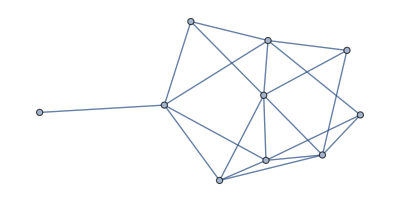
```mathematica
{-Graphics-,LinguisticAssistant,-Graphics-}
```

Here is a symbolic function called f applied to x:

```mathematica
f[x]
```

The function Framed displays with a frame around whatever it is applied to:

```mathematica
Framed[x]
```

This frames the list of objects:

```mathematica
Framed[{-Graphics-,LinguisticAssistant,-Graphics-}]
```

This instead puts a frame around each object:

```mathematica
Map[Framed,{-Graphics-,LinguisticAssistant,-Graphics-}]
```

The “pure function” puts a random background color behind each object:

```mathematica
Map[Framed[#,Background->RandomColor[]]&,{-Graphics-,LinguisticAssistant,-Graphics-}]
```

Successively apply a symbolic function f to x:

```mathematica
NestList[f,x,10]
```

If the function is Framed, this makes nested frames:

```mathematica
NestList[Framed,x,10]
```

Use a pure function to put a random background color inside each frame:

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

Create a graph of countries that share a border with Switzerland and their neighbors by nesting the "BorderingCountries" property twice:

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],2,VertexLabels->Automatic]
```

StringReverse reverses the characters in a string:

```mathematica
StringReverse["wolfram"]
```

The reversed string is not the same as the string itself:

```mathematica
StringReverse["wolfram"]=="wolfram"
```

This selects words in English that read the same backward and forward:

```mathematica
Select[WordList[],StringReverse[#]==#&]
```

The same result for Russian:

```mathematica
Select[WordList[Language->"Russian"],StringReverse[#]==#&]
```

You can define rules to give values to symbolic expressions:

```mathematica
fac[1]:=1
```

Now fac[1], i.e. factorial of 1, is 1:

```mathematica
fac[1]
```

The system does not yet know what fac[10], i.e. factorial of 10, is:

```mathematica
fac[10]
```

Define a generic rule to compute the factorial of any integer (represented by the pattern n_Integer):

```mathematica
fac[n_Integer]:=n*fac[n-1]
```

Now the rules allow you to compute fac[10]:

```mathematica
fac[10]
```

Or fac[1000]:

```mathematica
fac[1000]
```

You can also define a rule to catch erroneous inputs:

```mathematica
fac[anything_]:= "Input is not an integer"
```

```mathematica
fac["1.1"]
```

You can define rules for functions of arbitrary structures, here for a pair of elements:

```mathematica
myfunc[{x_,y_}]:={1-2x +y,y -x/4 }
```

```mathematica
myfunc[{6,7}]
```

It does not take too much Wolfram code to do pretty sophisticated things:

```mathematica
ImageTransformation[LinguisticAssistant["Image"],myfunc]
```

Make a simple piece of interactive graphics:

```mathematica
Manipulate[Graphics[{Yellow,Disk[],Black,Disk[{0,0},r]}],{r,0,1}]
```

Publish it to the cloud:

```mathematica
CloudPublish[Manipulate[Graphics[{Yellow,Disk[],Black,Disk[{0,0},r]}],{r,0,1}]]
```

Click the URL to visit the interactive website you have created.

This publishes a form interface to the cloud, putting more cats on the internet:

```mathematica
CloudPublish[FormPage[{{"breed","Enter a cat breed:"}->"CatBreed","color"->"Color","angle"->"Number"->0},ExportForm[Rotate[Blend[{#breed["Image"],#color}],#angle Degree],"PNG"]&]]
```

You can turn this into an API as well, and get the code to embed it in an external program:

```mathematica
EmbedCode[APIFunction[{"breed"->"CatBreed","color"->"Color","angle"->"Number"->0},ExportForm[Rotate[Blend[{#breed["Image"],#color}],#angle Degree],"PNG"]&],"Java"]
```

### Where to go next:

Fast Introduction for Programmershttp://www.wolfram.com/language/fast-introduction-for-programmers/Nonehttp://www.wolfram.com/language/fast-introduction-for-programmers/

An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introductionNonehttps://www.wolfram.com/language/elementary-introduction

Wolfram Uhttps://www.wolfram.com/wolfram-u/Nonehttps://www.wolfram.com/wolfram-u/

### See some larger programs:

Code Galleryhttps://www.wolfram.com/language/galleryNonehttps://www.wolfram.com/language/gallery

Wolfram Demonstrations Projecthttp://demonstrations.wolfram.com/Nonehttp://demonstrations.wolfram.com/

Notebook Archivehttps://notebookarchive.org/Nonehttps://notebookarchive.org/